```mathematica
Solve[{11.145 ==11.201+A/(3300+B),.65 ==11.201+A/(18+B)},{A,B}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{A→-184.773,B→-0.487661}}

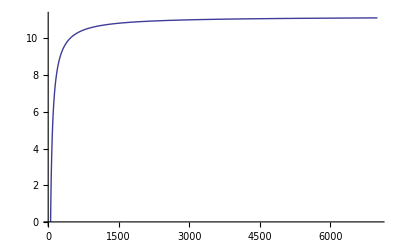

```mathematica
(*frequency->voltage mapping
Capacitor charged from current source*)
Plot[(11.201-185/(r/3-.488)),{r,50,7000},PlotRange->{0,11.2}]
```

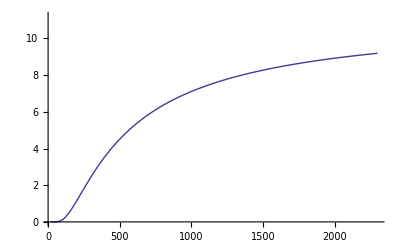

```mathematica
(*frequency->voltage mapping
Capacitor charged from resistor*)
R=100*10^3;
cap = .022*10^-6;
Plot[11.2*(Exp[-1/(r*R*cap)]),{r,17,2300},PlotRange->{0,11.2}]
```